# h=I+A+B (case 1)

Computation of the sequences η := (|| h_n((||)_2)^2), ξ:=(ξ_n) , ρ:=(η_n),  ζ:=(ζ_n), m:=(m_n) , tables, graphs, and densities for the paper
“A COMPUTATIONAL APPROACH TO THE THOMPSON GROUP F” 
by S. Haagerup, U. Haagerup, M. Ramirez-Solano:

```mathematica
η={0,0,0,0,0,0,0,400,800,1656,3344,7032,14272,30544,63120,137264,292160,651960,1435808,3310592,7593024,18161528,43488112,107764880,268721056,686850128,1769246208,4640551024,12254456800,32773003720,88160278544,239251904104,652453973392,1790526123576,4933923852880,13660080583776,37952694315360}

η={3,6,12,24,48,96,192,400,800,1656,3344,7032,14272,30544,63120,137264,292160,651960,1435808,3310592,7593024,18161528,43488112,107764880,268721056,686850128,1769246208,4640551024,12254456800,32773003720,88160278544,239251904104,652453973392,1790526123576,4933923852880,13660080583776,37952694315360}
```

{0,0,0,0,0,0,0,400,800,1656,3344,7032,14272,30544,63120,137264,292160,651960,1435808,3310592,7593024,18161528,43488112,107764880,268721056,686850128,1769246208,4640551024,12254456800,32773003720,88160278544,239251904104,652453973392,1790526123576,4933923852880,13660080583776,37952694315360}

{3,6,12,24,48,96,192,400,800,1656,3344,7032,14272,30544,63120,137264,292160,651960,1435808,3310592,7593024,18161528,43488112,107764880,268721056,686850128,1769246208,4640551024,12254456800,32773003720,88160278544,239251904104,652453973392,1790526123576,4933923852880,13660080583776,37952694315360}

```mathematica
q=3-1;
ξ=η-(q+1)Table[q^(n-1),{n,1,Length[η]}]
ρ=ξ-(q-1)Table[Total[ξ⟦Range[n-1]⟧],{n,1,Length[ξ]}]
ζ=ρ-(q-1)Table[Total[ρ⟦Range[n-1]⟧],{n,1,Length[ξ]}]
m=Table[Binomial[2n,n] q^n+Total[Table[Binomial[2n,n-k] q^(n-k)(ζ⟦k⟧+1-q),{k,1,n}]],{n,1,Length[ζ]}]
mq=Table[Binomial[2n,n] q^n+Total[Table[Binomial[2n,n-k] q^(n-k)(1-q),{k,1,n}]],{n,1,Length[ζ]}]
Ntuple=Length[m]
```

{0,0,0,0,0,0,0,16,32,120,272,888,1984,5968,13968,38960,95552,258744,649376,1737728,4447296,11870072,30905200,82599056,218389408,586186832,1567919616,4237897840,11449150432,31162390984,84939053072,232809453160,639569071504,1764756319800,4882384245328,13557001368672,37746535885152}

{0,0,0,0,0,0,0,16,16,72,104,448,656,2656,4688,15712,33344,100984,232872,671848,1643688,4619168,11784224,32572880,85764176,235172192,630718144,1732776752,4706131504,12970221624,35584492728,98515839744,272466004928,758084181720,2110955787448,5903188665464,16535721813272}

{0,0,0,0,0,0,0,16,0,40,0,240,0,1344,720,7056,8976,43272,74176,280280,580272,1912064,4457952,13462384,34080800,97724640,258098400,729438864,1970016864,5527975480,15172024960,42518879248,117953204688,331105376552,925892800560,2607169891128,7336514373472}

{3,15,87,543,3543,23823,163719,1144015,8100087,57971735,418640071,3046373007,22314896087,164407579407,1217526417687,9057960864015,67667981453831,507425879338551,3818200408513415,28821799875573303,218200189786794855,1656415132760705871,12606151256856370471,96166410605134544815,735237884585469467543,5632983879577272289359,43241777428163458121799,332564656181337723832623,2562203165206920141303479,19773205160010752987777543,152837887007013006956440295,1183157961642417140248556303,9172380845538923831902240519,71206765648586031626111809367,553521536480845628126004101879,4308220957036953495382444267287,33572939291063083015187615095255}

{3,15,87,543,3543,23823,163719,1143999,8099511,57959535,418441191,3043608351,22280372247,164008329423,1213166815047,9012417249663,67208553680247,502920171632943,3775020828459687,28415858155984863,214444848602732247,1622146752543427983,12297086677257812487,93407024378072517183,710817216408949234743,5418515848189548101103,41370969437551748377959,316342913595655481088159,2422290412177856021208471,18572165552209575045630543,142571626578134353530739911,1095738430841101539942155007,8430543922804728230924999415,64931174474685252212909028015,500582936483899929918138992679,3862797902645049762611593611615,29833954602139121152988918731863}

37

```mathematica
Grid[Transpose[{Range[Length[η]],η,ξ,ρ,ζ,m}],Alignment->Left]
```

1 | 3 | 0 | 0 | 0 | 3
2 | 6 | 0 | 0 | 0 | 15
3 | 12 | 0 | 0 | 0 | 87
4 | 24 | 0 | 0 | 0 | 543
5 | 48 | 0 | 0 | 0 | 3543
6 | 96 | 0 | 0 | 0 | 23823
7 | 192 | 0 | 0 | 0 | 163719
8 | 400 | 16 | 16 | 16 | 1144015
9 | 800 | 32 | 16 | 0 | 8100087
10 | 1656 | 120 | 72 | 40 | 57971735
11 | 3344 | 272 | 104 | 0 | 418640071
12 | 7032 | 888 | 448 | 240 | 3046373007
13 | 14272 | 1984 | 656 | 0 | 22314896087
14 | 30544 | 5968 | 2656 | 1344 | 164407579407
15 | 63120 | 13968 | 4688 | 720 | 1217526417687
16 | 137264 | 38960 | 15712 | 7056 | 9057960864015
17 | 292160 | 95552 | 33344 | 8976 | 67667981453831
18 | 651960 | 258744 | 100984 | 43272 | 507425879338551
19 | 1435808 | 649376 | 232872 | 74176 | 3818200408513415
20 | 3310592 | 1737728 | 671848 | 280280 | 28821799875573303
21 | 7593024 | 4447296 | 1643688 | 580272 | 218200189786794855
22 | 18161528 | 11870072 | 4619168 | 1912064 | 1656415132760705871
23 | 43488112 | 30905200 | 11784224 | 4457952 | 12606151256856370471
24 | 107764880 | 82599056 | 32572880 | 13462384 | 96166410605134544815
25 | 268721056 | 218389408 | 85764176 | 34080800 | 735237884585469467543
26 | 686850128 | 586186832 | 235172192 | 97724640 | 5632983879577272289359
27 | 1769246208 | 1567919616 | 630718144 | 258098400 | 43241777428163458121799
28 | 4640551024 | 4237897840 | 1732776752 | 729438864 | 332564656181337723832623
29 | 12254456800 | 11449150432 | 4706131504 | 1970016864 | 2562203165206920141303479
30 | 32773003720 | 31162390984 | 12970221624 | 5527975480 | 19773205160010752987777543
31 | 88160278544 | 84939053072 | 35584492728 | 15172024960 | 152837887007013006956440295
32 | 239251904104 | 232809453160 | 98515839744 | 42518879248 | 1183157961642417140248556303
33 | 652453973392 | 639569071504 | 272466004928 | 117953204688 | 9172380845538923831902240519
34 | 1790526123576 | 1764756319800 | 758084181720 | 331105376552 | 71206765648586031626111809367
35 | 4933923852880 | 4882384245328 | 2110955787448 | 925892800560 | 553521536480845628126004101879
36 | 13660080583776 | 13557001368672 | 5903188665464 | 2607169891128 | 4308220957036953495382444267287
37 | 37952694315360 | 37746535885152 | 16535721813272 | 7336514373472 | 33572939291063083015187615095255

```mathematica
μ=Function[d,If[d==1,1,Module[{k,factores,exponentes,isProductOfDistinctPrimes},
{factores,exponentes}=Transpose[FactorInteger[d]];
k=Length[factores];
If[Max[exponentes]==1 ,isProductOfDistinctPrimes=1,isProductOfDistinctPrimes=0];
If[isProductOfDistinctPrimes==1, (-1)^k,0]
]]]

ζpFunction=Function[n,Module[{divisors,i},
divisors=Divisors[n];
Total[Table[μ[n/divisors⟦i⟧]ζ[[divisors⟦i⟧]],{i,1,Length[divisors]}]]
]]
```

Function[d,If[d==1,1,Module[{k,factores,exponentes,isProductOfDistinctPrimes},{factores,exponentes}=Transpose[FactorInteger[d]];k=Length[factores];If[Max[exponentes]==1,isProductOfDistinctPrimes=1,isProductOfDistinctPrimes=0];If[isProductOfDistinctPrimes==1,(-1)^k,0]]]]

Function[n,Module[{divisors,i},divisors=Divisors[n];Total[Table[μ[n/divisors⟦i⟧] ζ⟦divisors⟦i⟧⟧,{i,1,Length[divisors]}]]]]

```mathematica
Table[{n,ζpFunction[n]},{n,1,Length[ζ]}]//ColumnForm
```

{1,0}
{2,0}
{3,0}
{4,0}
{5,0}
{6,0}
{7,0}
{8,16}
{9,0}
{10,40}
{11,0}
{12,240}
{13,0}
{14,1344}
{15,720}
{16,7040}
{17,8976}
{18,43272}
{19,74176}
{20,280240}
{21,580272}
{22,1912064}
{23,4457952}
{24,13462128}
{25,34080800}
{26,97724640}
{27,258098400}
{28,729437520}
{29,1970016864}
{30,5527974720}
{31,15172024960}
{32,42518872192}
{33,117953204688}
{34,331105367576}
{35,925892800560}
{36,2607169847616}
{37,7336514373472}

```mathematica
Table[{n,ζpFunction[n]/(2n)},{n,1,Length[ζ]}]//ColumnForm
```

{1,0}
{2,0}
{3,0}
{4,0}
{5,0}
{6,0}
{7,0}
{8,1}
{9,0}
{10,2}
{11,0}
{12,10}
{13,0}
{14,48}
{15,24}
{16,220}
{17,264}
{18,1202}
{19,1952}
{20,7006}
{21,13816}
{22,43456}
{23,96912}
{24,280461}
{25,681616}
{26,1879320}
{27,4779600}
{28,13025670}
{29,33965808}
{30,92132912}
{31,244710080}
{32,664357378}
{33,1787169768}
{34,4869196582}
{35,13227040008}
{36,36210692328}
{37,99142086128}

```mathematica
mm=Riffle[0Range[Length[m]],m]
Table[d[n]=Det[Table[If[i+j==0,1,mm⟦i+j⟧],{i,0,n},{j,0,n}]],{n,0,Length[m]}]
d[-1]=1;
Table[k[n]=(d[n-1]/d[n])^(1/2),{n,0,Length[m]}]
Table[α[n]=k[n-1]/k[n],{n,1,Length[m]}]
```

{0,3,0,15,0,87,0,543,0,3543,0,23823,0,163719,0,1144015,0,8100087,0,57971735,0,418640071,0,3046373007,0,22314896087,0,164407579407,0,1217526417687,0,9057960864015,0,67667981453831,0,507425879338551,0,3818200408513415,0,28821799875573303,0,218200189786794855,0,1656415132760705871,0,12606151256856370471,0,96166410605134544815,0,735237884585469467543,0,5632983879577272289359,0,43241777428163458121799,0,332564656181337723832623,0,2562203165206920141303479,0,19773205160010752987777543,0,152837887007013006956440295,0,1183157961642417140248556303,0,9172380845538923831902240519,0,71206765648586031626111809367,0,553521536480845628126004101879,0,4308220957036953495382444267287,0,33572939291063083015187615095255}

{1,3,18,216,5184,248832,23887872,4586471424,1834588569600,1465224737587200,2418753924149280768,8020819523706034323456,55621455490265529779748864,771257589297244616685105709056,22573616473892003259921831624179712,1323041867885128332176009815756573245440,163573549074771221819290690208631917044039680,40768217085427869104745510825374464332475372929024,21481190983733202819162530507600327688146718150671466496,22837201998927496678236450191436488430582405591356001161838592,51449102309117687885760082869028612233504308745305071878330663305216,234153866021884557163454624665557448380732756615203713543025282144133971968,2264386863252566562087442955121814099428228945443312703141399167456886015444123648,44321998812089241420401035177498510846589482285979255997314860566125518097642318035156992,1844356742848274409001680674450161496069646719285577673387459438469088170293398985808974465466368,156148813265513459714101313166058667243945354846168950500164843008592551760207484251329502319191238115328,28024066373624899479750794764818355503420220655479573536260779835020535104561942507349059044269815214899250331648,10261873501676642143863104639679774521762832082656958686451938306715996079680639182963682312574047158053513500707300311040,7986372193761184872154254897785610865354327886034818307922160257248139071208863723526960630973434091403690539279056209452162088960,12689244939837692916561260786571127920189525564695535351525533525614930263093628957190712085673770124727550204930656569626123232294656278528,42867274401831078879590618247071823317370307120423327195137465383775626371831251049827678053877979129112197534915413075312652637358879301462218768384,296367122888460807331110729996130493508930521917748019844857239648494844937044275467778144727148524075996782655357501965382796730686184483140580696043267555328,4358822230321170818306246244632176328859001305629503420436622679778394911190890290024340722320187102914020534501555468441002822982878316657300122119018429752223859736576,131420589758915372391479480714488244227538539297538167552757211238151744637152210104378918694653306652584236292533687594885233073451657659957993549721608786998383405678933089189888,8430074969423268004171739410572180206670240577342208605145853834511294719913585374321371591485259473648831182603452623387925350059802014442331096057335766717531088806736441268530732110708736,1111113316417338669984809008714934456399580836701564864200666679175617166503808418619467624679109003794140723273670661931964827904282653911392463905817260166703135268078566982435274717364347830483812352,311340582498361610117361139820733982814294106902850258759316406103887681327709718358502932397075115776101858892373442843710235576698852778391592285661389309815437478727838396067237792983247076107290320400698834944,179703984806919284308196197113750780327412739797728913168299507560623784116562584347585374940141254855923236496162403052835155975931167218565507147498402238209445788451339399566622920371179959868243895349967761776449758953472}

{1,1/(√3),1/(√6),1/(2 √3),1/(2 √6),1/(4 √3),1/(4 √6),1/(8 √3),1/20,(√(3/599))/2,(5 √(3/7738))/4,(√(1797/372439))/4,(√(11607/20122577))/2,√(1117317/15492928193),√(120735462/3533755844749),(√(46478784579/681031526755495))/2,(√(3533755844749/3033985750313262))/12,(√(681031526755495/2652136577268463069))/8,(3 √(1516992875156631/449616981095932586851))/4,(√(2652136577268463069/704888509087894471227697))/2,(√(449616981095932586851/63307859642261657406444203))/4,(√(704888509087894471227697/200504433155195459612351514791))/4,(√(63307859642261657406444203/153054792720330826889917966282527))/2,√(200504433155195459612351514791/3924575518583541317160840308241161839),√(153054792720330826889917966282527/6369018693759599584770112292838940884883),(√(3924575518583541317160840308241161839/20766651170319451879538837117410043457356159))/4,(√(6369018693759599584770112292838940884883/285762342466992982072949973422544850055668650882))/2,(√(20766651170319451879538837117410043457356159/1901086949000278291400024111606796051842511059807205))/2,(√(47627057077832163678824995570424141675944775147/9266519516512483697182742550445951166585945535918491682))/2,(√(633695649666759430466674703868932017280837019935735/62928441732066008679742534768806506376328038154050661867303))/4,(√(4633259758256241848591371275222975583292972767959245841/3913062171425629359723824487282780330546492871365372956704555562))/2,(√(188785325196198026039227604306419519128984114462151985601909/326296484046870952645147136743869729339249167863130357381132343034907))/2,(√(5869593257138444039585736730924170495819739307048059435056833343/21581774424576737649468270267854331895904975102875833439702192078693802114))/2,(√(326296484046870952645147136743869729339249167863130357381132343034907/614874760081415166856589409301938967937321125666883093828582245747696976965326))/4,(√(10790887212288368824734135133927165947952487551437916719851096039346901057/10815465202344115914753824558534983432461303507426524066664392289469669759555819786))/8,(√(307437380040707583428294704650969483968660562833441546914291122873848488482663/2532582510881411734028508979056820168589440906603567459495422358880420880940532905348601))/4,(√(5407732601172057957376912279267491716230651753713262033332196144734834879777909893/168364327639018656297770385618995465404166376665327362698718720677722899974379175668005738494))/3,(√(2532582510881411734028508979056820168589440906603567459495422358880420880940532905348601/7458122388121271722746532161502187079545027925138021021348479056951798450976087126537086452786278))/14}

{√3,√2,√2,√2,√2,√2,√2,5/(2 √3),(√(599/3))/10,(2 √(7738/599))/5,5 √(372439/4635062),(√(12053423623/1440966491))/2,(√(59942139178717/7494432455303))/2,√(1316108493062472811/623515281038226722),2 √(27408218673130016621230/54748225554290313108557),18 √(15668441122729531807198522/2406599138130565428902645755),(√(18744006261990078446702008149362/1033119973845128431165364937345))/3,(√(306203339090959503149335654328996245/4023272291658552242107770013960539))/6,(3 √(1069310846066116053671254850581740408807/1192445641325545914133295394710128505719))/2,2 √(167901090185820098903656432934273722114639007/316929843465311953918334827876530763049212147),√(90150197931590195963484230782249040456029018613141/44624982796779503924911108582650024820176738690491),(√(107886564649390720628189628497725812952395198376849550319/12693506511840348830174382938060697916488569072070706573))/2,(√(248456476085943090609713266607330983153960021214660578446369317/30688164456075868920089090725338656660449163503724471525356857))/2,√(1277016482947111936509046538692495733744258906065378978947207002804453/600675092512088779414669374938721822779521282360837525006150204887153),4 √(3178435490368659290227519203171882662010966096698503884469842102729057533793/24995694842929849465450239715573974519445743157385369330006919778574671579837),√(560747946689523257119734286383792204224152260107659645149822547323604827938676045999/264526379021098510816674519924867418960183806916842036640493597382144577414300088794),√(4036019438881724985733781914228960801217258167989636174335981828065154230578410232692994005/1978108961208469271649839117136344414625213185180642437888400631421703184833052756701160746),√(64144859454124003655346385132583528746522217966170730205746037611992824666539726856546739584323146/30181058876652685927546414973528156433347608484796503967774616226791887934091010371048950965178045),√(5994192972384286600192311086205934218059587125399161322091616506697497437089803236348362689727306972637082/2936076552583041924163163490593381357267306911812169903411291480229509751484116418653494485500932886028135),√(1239845237453992278572042734291125787525101872758317415179952002051254809819239602186407765774214632696943488404035/583127633453908312907857567804389753786800024459921398719062122624726548828204104951258402358113122873817393273646),√(503938789598288994990306327353059714858691833476532704540209928658683973951082993000087293301285748788868577768162952523929/246242904848509408602495418915733218015083392341303039062117884874117809391286898482812876928559295615110583506057634589286),√(1358107434351569648373482199802657583022680658628762708572076856199438892892307752781918123704930936355279138947646860692268008878542/638409214196498539649731221159437181585455444809685989022771124022340278837659448061484774324679493283467035236895763959213843501367),6 √(200503596986582943334663827738312832239849535748484059968051950830751408769308533546675685707730571977465303566335986972751818661263526203601/3521028557116035505132252462257592924849464591601317678900096852004178190669919606052127425489340210290228173335212478706234148089068826196699),2 √(1764524134428082369203462215685471964655562249249769649976485404076747418104860598199306075193844893909884256842244625095950279931058799310376799634951/3317522092860710857409488947516964637340997228237009756505241296032877316939924011793616247274689824514394426394427602550827493507083517784345120874791),(√(27328812230735394571440080491540541910437573113306695746777875598892555820177430504072252100513579342065515447613257940406047961166377391654617244300149640371257/3325078285730116307288460534917925216105443955681758244590092233992067618158045625570353304602390308159197742271841972133802388355354666631215778753074213370118))/2,(3 √(25880743890827593188510561582998079267349294534349342288288015756375877294033734165836619918123132885973835814155455646474604158107216067152693670312415445875975415364761/27391058018503196905441312976617730659019074610382855341210774503748421051489049747416086756032533131106999013741753778842739137283150684258481877958634720833976663219386))/2,(14 √(20165765790887302770321510109335354983127472845974611225737167188785299273875582409326668103324380712807977009177262128601011419228654725180804104036062451210459095004542535424127/213198275817443268238143042805483823654043781086177070679340632888485060812476436827733340140471239657015707466293218282515558628969845816207459404215600649220331259737306757373447))/3}

```mathematica
MnormFunctiontest=Function[n,Module[{i,j,eigenvalues,A},
A=Table[0,{i,1,n+1},{j,1,n+1}];
Table[A⟦i,i+1⟧=α[i]^2,{i,1,n}];
Table[A⟦i+1,i⟧=1,{i,1,n}];
A
]];
Table[(MnormFunctiontest[i]//MatrixForm),{i,0,7}]
MnormFunction=Function[n,Module[{i,j,eigenvalues,A},
A=Table[0,{i,1,n+1},{j,1,n+1}];
Table[A⟦i,i+1⟧=α[i]^2,{i,1,n}];
Table[A⟦i+1,i⟧=1,{i,1,n}];
eigenvalues=Eigenvalues[A];
eigenvalues=eigenvalues//N;
Max[eigenvalues]
]];
Table[Mnorm[i]=MnormFunction[i],{i,0,Length[m]}]
```

{(0),(0 | 3
1 | 0),(0 | 3 | 0
1 | 0 | 2
0 | 1 | 0),(0 | 3 | 0 | 0
1 | 0 | 2 | 0
0 | 1 | 0 | 2
0 | 0 | 1 | 0),(0 | 3 | 0 | 0 | 0
1 | 0 | 2 | 0 | 0
0 | 1 | 0 | 2 | 0
0 | 0 | 1 | 0 | 2
0 | 0 | 0 | 1 | 0),(0 | 3 | 0 | 0 | 0 | 0
1 | 0 | 2 | 0 | 0 | 0
0 | 1 | 0 | 2 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0
0 | 0 | 0 | 1 | 0 | 2
0 | 0 | 0 | 0 | 1 | 0),(0 | 3 | 0 | 0 | 0 | 0 | 0
1 | 0 | 2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 2 | 0 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0 | 0
0 | 0 | 0 | 1 | 0 | 2 | 0
0 | 0 | 0 | 0 | 1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

{0.,1.73205,2.23607,2.44949,2.56155,2.6286,2.67233,2.70265,2.7262,2.74445,2.75941,2.77154,2.782,2.79072,2.7985,2.80515,2.81118,2.81645,2.82132,2.82563,2.82966,2.83326,2.83665,2.83972,2.84263,2.84529,2.84782,2.85014,2.85237,2.85443,2.85641,2.85824,2.86002,2.86167,2.86327,2.86477,2.86623,2.86759}

{1.73205,1.41421,1.41421,1.41421,1.41421,1.41421,1.41421,1.44338,1.41303,1.43768,1.41733,1.4461,1.41406,1.45286,1.41509,1.45239,1.41982,1.454,1.42044,1.45571,1.42133,1.45768,1.42269,1.45807,1.42638,1.45596,1.42841,1.45785,1.42883,1.45815,1.43056,1.45854,1.43178,1.4586,1.43344,1.45806,1.43523}

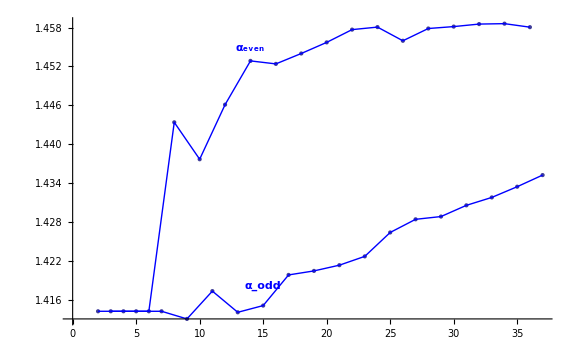

```mathematica
Table[α[n],{n,1,Ntuple}]//N
Show[
ListPlot[Table[{i,α[i]},{i,2,Ntuple}],Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],
ListPlot[Table[{i,α[i]},{i,2,Ntuple,2}],Joined->True,PlotStyle->{Blue}],ListPlot[Table[{i,α[i]},{i,3,Ntuple,2}],Joined->True,PlotStyle->{Blue}],
Graphics[{Blue,Text[Style[HoldForm[Subscript[α, even]],Large,Bold],{14,.002+α[14]}]}],
Graphics[{Blue,Text[Style[HoldForm[Subscript[α, odd]],Large,Bold],{15,.003+α[15]}]}]
]
```

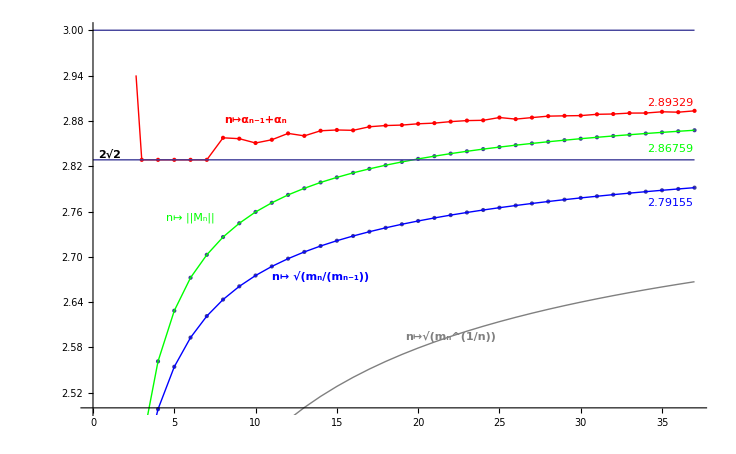

```mathematica
ma[0]=1;
Table[ma[i]=m⟦i⟧,{i,1,Length[m]}];
Show[
ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotRange->{2.5,3}],
ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Joined->True,PlotStyle->{Green}],
Graphics[{Green,Text[Style[HoldForm["n↦ ||M_n||"],Large],{6,.08+Mnorm[6]}]}],
Graphics[{Green,Text[Style[N[Mnorm[Ntuple],6],Large],{Ntuple-1.5,-.025+Mnorm[Ntuple]}]}],
Graphics[{Red,Text[Style[N[α[Ntuple-1]+α[Ntuple],6],Large],{Ntuple-1.5,.01+α[Ntuple-1]+α[Ntuple]}]}],
Graphics[{Blue,Text[Style[N[(ma[Ntuple]/ma[Ntuple-1])^(1/2),6],Large],{Ntuple-1.5,-.02+(ma[Ntuple]/ma[Ntuple-1])^(1/2)}]}],
Plot[8,{x,0,Ntuple}],
ListPlot[Table[{i,(ma[i]/ma[i-1])^(1/2)},{i,1,Ntuple}],Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],
ListPlot[Table[{i,(ma[i]/ma[i-1])^(1/2)},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Blue}],
Graphics[{Blue,Text[Style[HoldForm[n↦(Subscript[m, n]/Subscript[m, n-1])^(1/2)],Large,Bold],{14,-.04+(ma[14]/ma[13])^(1/2)}]}],
ListPlot[Table[{i,α[i-1]+α[i]},{i,1,Ntuple}],PlotStyle->{Red},Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],
ListPlot[Table[{i,α[i-1]+α[i]},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Red}],
Graphics[{Red,Text[Style[HoldForm[n↦Subscript[α, n-1]+Subscript[α, n]],Large,Bold],{10,.03+α[9]+α[10]}]}],
ListPlot[Table[{i,(ma[i]^(1/i))^(1/2)},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Gray}],
Graphics[{Gray,Text[Style[HoldForm[n↦√((Subscript[m, n])^(1/n))],Large,Bold],{22,-.00+(ma[22]^(1/(2 22)))}]}],
Graphics[{Black,Text[Style[HoldForm["2√2"],Medium,Bold],{1,2Sqrt[2]+.007}]}],
Plot[Sqrt[8],{x,0,Ntuple}],
Plot[3,{x,0,Ntuple}]

]
```

```mathematica
Grid[Transpose[
{Range[Length[η]],
N[Table[(ma[i]^(1/i))^(1/2),{i,1,Ntuple,1}],6],
N[Table[(ma[i]/ma[i-1])^(1/2),{i,1,Ntuple}],6],
N[Table[α[n],{n,1,Ntuple}],6],
N[Table[Mnorm[i],{i,1,Ntuple}],6],
N[Table[α[i-1]+α[i],{i,1,Ntuple}],6]}
],Alignment->Left]
```

1 | 1.73205 | 1.73205 | 1.73205 | 1.73205 | 1.73205+α[0]
2 | 1.96799 | 2.23607 | 1.41421 | 2.23607 | 3.14626
3 | 2.10501 | 2.40832 | 1.41421 | 2.44949 | 2.82843
4 | 2.1971 | 2.49828 | 1.41421 | 2.56155 | 2.82843
5 | 2.26432 | 2.55438 | 1.41421 | 2.6286 | 2.82843
6 | 2.31606 | 2.59306 | 1.41421 | 2.67233 | 2.82843
7 | 2.35741 | 2.62151 | 1.41421 | 2.70265 | 2.82843
8 | 2.3914 | 2.64342 | 1.44338 | 2.7262 | 2.85759
9 | 2.41994 | 2.6609 | 1.41303 | 2.74445 | 2.85641
10 | 2.44434 | 2.67524 | 1.43768 | 2.75941 | 2.85071
11 | 2.46548 | 2.68728 | 1.41733 | 2.77154 | 2.855
12 | 2.48403 | 2.69756 | 1.4461 | 2.782 | 2.86343
13 | 2.50048 | 2.70649 | 1.41406 | 2.79072 | 2.86016
14 | 2.51518 | 2.71434 | 1.45286 | 2.7985 | 2.86691
15 | 2.52842 | 2.72131 | 1.41509 | 2.80515 | 2.86795
16 | 2.54043 | 2.72757 | 1.45239 | 2.81118 | 2.86749
17 | 2.55138 | 2.73323 | 1.41982 | 2.81645 | 2.87222
18 | 2.56143 | 2.73839 | 1.454 | 2.82132 | 2.87382
19 | 2.57069 | 2.74311 | 1.42044 | 2.82563 | 2.87444
20 | 2.57925 | 2.74746 | 1.45571 | 2.82966 | 2.87615
21 | 2.5872 | 2.75148 | 1.42133 | 2.83326 | 2.87704
22 | 2.59461 | 2.75522 | 1.45768 | 2.83665 | 2.87901
23 | 2.60154 | 2.75871 | 1.42269 | 2.83972 | 2.88037
24 | 2.60803 | 2.76198 | 1.45807 | 2.84263 | 2.88076
25 | 2.61414 | 2.76505 | 1.42638 | 2.84529 | 2.88445
26 | 2.61989 | 2.76793 | 1.45596 | 2.84782 | 2.88234
27 | 2.62533 | 2.77066 | 1.42841 | 2.85014 | 2.88437
28 | 2.63047 | 2.77323 | 1.45785 | 2.85237 | 2.88626
29 | 2.63535 | 2.77568 | 1.42883 | 2.85443 | 2.88669
30 | 2.63998 | 2.778 | 1.45815 | 2.85641 | 2.88698
31 | 2.64439 | 2.78021 | 1.43056 | 2.85824 | 2.88871
32 | 2.6486 | 2.78231 | 1.45854 | 2.86002 | 2.8891
33 | 2.65261 | 2.78432 | 1.43178 | 2.86167 | 2.89032
34 | 2.65645 | 2.78625 | 1.4586 | 2.86327 | 2.89039
35 | 2.66012 | 2.78809 | 1.43344 | 2.86477 | 2.89204
36 | 2.66365 | 2.78986 | 1.45806 | 2.86623 | 2.8915
37 | 2.66702 | 2.79155 | 1.43523 | 2.86759 | 2.89329

Function[x,(3 √(8-x^2))/((2 π) (9-x^2))]

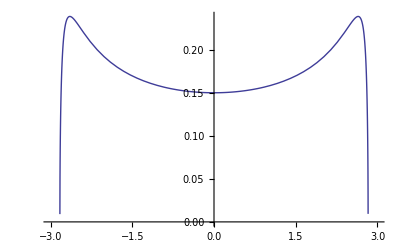

Function[n,Module[{coeffs,mlist},If[Mod[n,2]==0&&n≤2 Ntuple,coeffs=CoefficientList[LegendreP[n,x/(q+1)],x];coeffs=coeffs⟦Range[1,Length[coeffs],2]⟧;mlist=Table[ma[i],{i,0,n/2}];√((2 n+1)/(2 (q+1))) coeffs.mlist,0]]]

Function[n,√((2 n+1)/(2 (q+1))) LegendreP[n,x/(q+1)]]

```mathematica
ρFree=Function[x,3/(2π)(√(8-x^2))/(9-x^2)]
(*Integrate[ρFree[x],{x,-√8,√8}]==1*)
Plot[ρFree[x],{x,-(q+1),(q+1)}]
ρLebesgueCoords=Function[n,Module[{coeffs,mlist},
If[Mod[n,2]==0 &&n≤2Ntuple,
coeffs=CoefficientList[LegendreP[n,x/(q+1)],x];
coeffs=coeffs⟦Range[1,Length[coeffs],2]⟧;
mlist=Table[ma[i],{i,0,n/2}];
√((2n+1)/(2(q+1)))coeffs.mlist,0]]]
p=Function[n,√((2 n+1)/(2(q+1))) LegendreP[n,x/(q+1)]]
ρLebesgue=Total[Table[ρLebesgueCoords[i]p[i],{i,0,2Ntuple}]];
ρLebesgueNminus1=Total[Table[ρLebesgueCoords[i]p[i],{i,0,2(Ntuple-1)}]];
ρLebesgueGraph=Table[{x,ρLebesgue},{x,0,q+1,1/100}];
ρLebesgueGraphTail=Table[{x,ρLebesgue},{x,27/10,q+1,1/1000}];
ρLebesgueGraphTailNminus1=Table[{x,ρLebesgueNminus1},{x,27/10,q+1,1/1000}];
```

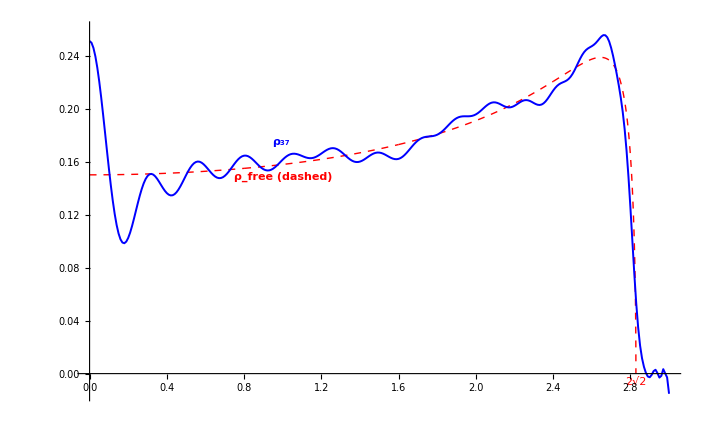

```mathematica
Show[
ListPlot[Join[Table[{x,ρFree[x]},{x,0,2Sqrt[2],1/10000}],{{2Sqrt[2],0}}],Joined->True,PlotStyle->{Dashed,Red},PlotRange->{{0,q+1},{-.015,.26}},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],ListPlot[ρLebesgueGraph,Joined->True,PlotStyle->{Directive[Blue,Thickness[.002]]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,Thickness[.002]]}],
Graphics[{Blue,Text[Style[HoldForm[Subscript[ρ, 37]],Large,Bold],Evaluate[ρLebesgueGraph⟦100⟧+{0,.015}]]}],
Graphics[{Red,Text[Style[HoldForm["2√2"],Medium],{2Sqrt[2],-.006}]}],
Graphics[{Red,Text[Style[HoldForm[Subscript[ρ, free]"(dashed)"],Large,Bold],Evaluate[{1,ρFree[0.7]-.005}]]}]
]
```

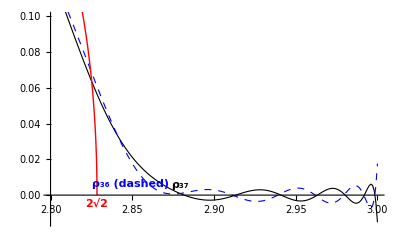

```mathematica
Show[ListPlot[Table[{x,ρFree[x]},{x,3.43,3.5,1/10000}],Joined->True,PlotStyle->{Red},PlotRange->{{2.8,q+1},{-.015,.10}},AxesOrigin->{2.8,0},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotRange->{2.8,q+1}],
ListPlot[ρLebesgueGraphTail,Joined->True,PlotStyle->{Directive[Black,Thickness[.002]]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,Thickness[.002]]}],
Graphics[{Black,Text[Style[HoldForm[Subscript[ρ, 37]],Large,Bold],Evaluate[ρLebesgueGraphTail⟦170⟧+{.01,.00}]]}],
Graphics[{Red,Text[Style[HoldForm["2√2"],Medium,Bold],{2Sqrt[2],-.005}]}],
ListPlot[ρLebesgueGraphTailNminus1,Joined->True,PlotStyle->{Dashed,Directive[Blue,Thickness[.002]]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,Thickness[.002]]}],
Graphics[{Blue,Text[Style[HoldForm[Subscript[ρ, 36]"(dashed)"],Large,Bold],Evaluate[ρLebesgueGraphTailNminus1⟦170⟧+{-.02,0.005}]]}],ListPlot[Join[Table[{x,ρFree[x]},{x,28/10,Sqrt[8],1/10000}],{{Sqrt[8],0}}],Joined->True,PlotStyle->{Red},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}]]
```

```mathematica
(ρLebesgueGraphTail+ρLebesgueGraphTailNminus1)/2//N//ColumnForm
```

{2.7,0.24639}
{2.701,0.24597}
{2.702,0.245536}
{2.703,0.245088}
{2.704,0.244626}
{2.705,0.24415}
{2.706,0.24366}
{2.707,0.243156}
{2.708,0.242637}
{2.709,0.242105}
{2.71,0.241559}
{2.711,0.240998}
{2.712,0.240424}
{2.713,0.239835}
{2.714,0.239233}
{2.715,0.238616}
{2.716,0.237985}
{2.717,0.237341}
{2.718,0.236683}
{2.719,0.23601}
{2.72,0.235325}
{2.721,0.234625}
{2.722,0.233911}
{2.723,0.233184}
{2.724,0.232444}
{2.725,0.231689}
{2.726,0.230921}
{2.727,0.23014}
{2.728,0.229345}
{2.729,0.228537}
{2.73,0.227715}
{2.731,0.226879}
{2.732,0.22603}
{2.733,0.225168}
{2.734,0.224292}
{2.735,0.223402}
{2.736,0.222499}
{2.737,0.221582}
{2.738,0.220651}
{2.739,0.219706}
{2.74,0.218747}
{2.741,0.217774}
{2.742,0.216787}
{2.743,0.215785}
{2.744,0.214769}
{2.745,0.213738}
{2.746,0.212693}
{2.747,0.211632}
{2.748,0.210555}
{2.749,0.209463}
{2.75,0.208355}
{2.751,0.207231}
{2.752,0.20609}
{2.753,0.204933}
{2.754,0.203759}
{2.755,0.202567}
{2.756,0.201357}
{2.757,0.200129}
{2.758,0.198883}
{2.759,0.197618}
{2.76,0.196334}
{2.761,0.19503}
{2.762,0.193706}
{2.763,0.192362}
{2.764,0.190997}
{2.765,0.18961}
{2.766,0.188203}
{2.767,0.186773}
{2.768,0.18532}
{2.769,0.183845}
{2.77,0.182346}
{2.771,0.180824}
{2.772,0.179279}
{2.773,0.177708}
{2.774,0.176113}
{2.775,0.174494}
{2.776,0.172849}
{2.777,0.171178}
{2.778,0.169482}
{2.779,0.167759}
{2.78,0.166011}
{2.781,0.164236}
{2.782,0.162435}
{2.783,0.160607}
{2.784,0.158753}
{2.785,0.156872}
{2.786,0.154964}
{2.787,0.15303}
{2.788,0.15107}
{2.789,0.149084}
{2.79,0.147071}
{2.791,0.145033}
{2.792,0.14297}
{2.793,0.140882}
{2.794,0.138769}
{2.795,0.136633}
{2.796,0.134473}
{2.797,0.13229}
{2.798,0.130086}
{2.799,0.12786}
{2.8,0.125613}
{2.801,0.123348}
{2.802,0.121063}
{2.803,0.118761}
{2.804,0.116443}
{2.805,0.11411}
{2.806,0.111762}
{2.807,0.109401}
{2.808,0.107029}
{2.809,0.104647}
{2.81,0.102256}
{2.811,0.0998579}
{2.812,0.0974543}
{2.813,0.0950466}
{2.814,0.0926365}
{2.815,0.0902257}
{2.816,0.087816}
{2.817,0.0854092}
{2.818,0.0830069}
{2.819,0.0806111}
{2.82,0.0782237}
{2.821,0.0758465}
{2.822,0.0734814}
{2.823,0.0711304}
{2.824,0.0687953}
{2.825,0.0664781}
{2.826,0.0641808}
{2.827,0.0619052}
{2.828,0.0596532}
{2.829,0.0574268}
{2.83,0.0552278}
{2.831,0.0530581}
{2.832,0.0509194}
{2.833,0.0488136}
{2.834,0.0467423}
{2.835,0.0447072}
{2.836,0.04271}
{2.837,0.0407521}
{2.838,0.0388352}
{2.839,0.0369606}
{2.84,0.0351296}
{2.841,0.0333435}
{2.842,0.0316035}
{2.843,0.0299108}
{2.844,0.0282661}
{2.845,0.0266706}
{2.846,0.0251249}
{2.847,0.0236298}
{2.848,0.0221858}
{2.849,0.0207935}
{2.85,0.0194531}
{2.851,0.018165}
{2.852,0.0169293}
{2.853,0.0157459}
{2.854,0.0146149}
{2.855,0.0135359}
{2.856,0.0125087}
{2.857,0.0115329}
{2.858,0.0106078}
{2.859,0.00973285}
{2.86,0.00890727}
{2.861,0.00813016}
{2.862,0.00740057}
{2.863,0.00671741}
{2.864,0.00607952}
{2.865,0.00548566}
{2.866,0.00493447}
{2.867,0.00442455}
{2.868,0.00395442}
{2.869,0.00352252}
{2.87,0.00312724}
{2.871,0.00276692}
{2.872,0.00243986}
{2.873,0.00214432}
{2.874,0.00187853}
{2.875,0.0016407}
{2.876,0.00142903}
{2.877,0.00124172}
{2.878,0.00107696}
{2.879,0.000932969}
{2.88,0.000807978}
{2.881,0.000700248}
{2.882,0.000608077}
{2.883,0.000529808}
{2.884,0.000463835}
{2.885,0.000408611}
{2.886,0.000362656}
{2.887,0.00032456}
{2.888,0.000292995}
{2.889,0.000266712}
{2.89,0.000244553}
{2.891,0.000225451}
{2.892,0.000208436}
{2.893,0.000192637}
{2.894,0.000177283}
{2.895,0.000161707}
{2.896,0.000145343}
{2.897,0.000127731}
{2.898,0.000108511}
{2.899,0.0000874243}
{2.9,0.0000643088}
{2.901,0.0000390982}
{2.902,0.0000118161}
{2.903,-0.0000174287}
{2.904,-0.0000484475}
{2.905,-0.0000809785}
{2.906,-0.000114694}
{2.907,-0.000149206}
{2.908,-0.00018408}
{2.909,-0.000218835}
{2.91,-0.000252963}
{2.911,-0.000285929}
{2.912,-0.000317188}
{2.913,-0.000346191}
{2.914,-0.000372396}
{2.915,-0.000395279}
{2.916,-0.000414343}
{2.917,-0.000429127}
{2.918,-0.000439218}
{2.919,-0.000444256}
{2.92,-0.000443946}
{2.921,-0.000438061}
{2.922,-0.000426454}
{2.923,-0.00040906}
{2.924,-0.000385902}
{2.925,-0.000357093}
{2.926,-0.000322839}
{2.927,-0.000283442}
{2.928,-0.000239296}
{2.929,-0.000190886}
{2.93,-0.000138787}
{2.931,-0.0000836553}
{2.932,-0.0000262225}
{2.933,0.0000327109}
{2.934,0.000092287}
{2.935,0.000151601}
{2.936,0.000209714}
{2.937,0.000265668}
{2.938,0.000318498}
{2.939,0.000367252}
{2.94,0.000411006}
{2.941,0.00044888}
{2.942,0.000480058}
{2.943,0.000503807}
{2.944,0.00051949}
{2.945,0.000526587}
{2.946,0.000524711}
{2.947,0.000513621}
{2.948,0.000493237}
{2.949,0.00046365}
{2.95,0.000425132}
{2.951,0.000378142}
{2.952,0.000323327}
{2.953,0.000261526}
{2.954,0.000193759}
{2.955,0.000121224}
{2.956,0.0000452794}
{2.957,-0.0000325689}
{2.958,-0.000110694}
{2.959,-0.000187374}
{2.96,-0.000260824}
{2.961,-0.000329231}
{2.962,-0.000390799}
{2.963,-0.000443788}
{2.964,-0.000486567}
{2.965,-0.000517662}
{2.966,-0.000535809}
{2.967,-0.000540006}
{2.968,-0.000529564}
{2.969,-0.000504159}
{2.97,-0.000463875}
{2.971,-0.000409244}
{2.972,-0.000341278}
{2.973,-0.000261489}
{2.974,-0.000171898}
{2.975,-0.0000750287}
{2.976,0.0000261207}
{2.977,0.000128119}
{2.978,0.000227174}
{2.979,0.000319223}
{2.98,0.000400058}
{2.981,0.000465476}
{2.982,0.000511456}
{2.983,0.000534377}
{2.984,0.000531253}
{2.985,0.000500009}
{2.986,0.000439766}
{2.987,0.000351157}
{2.988,0.000236647}
{2.989,0.000100848}
{2.99,-0.0000491751}
{2.991,-0.000203644}
{2.992,-0.00034986}
{2.993,-0.000472089}
{2.994,-0.000551583}
{2.995,-0.000566766}
{2.996,-0.000493654}
{2.997,-0.000306577}
{2.998,0.0000207364}
{2.999,0.000513595}
{3.,0.00119421}

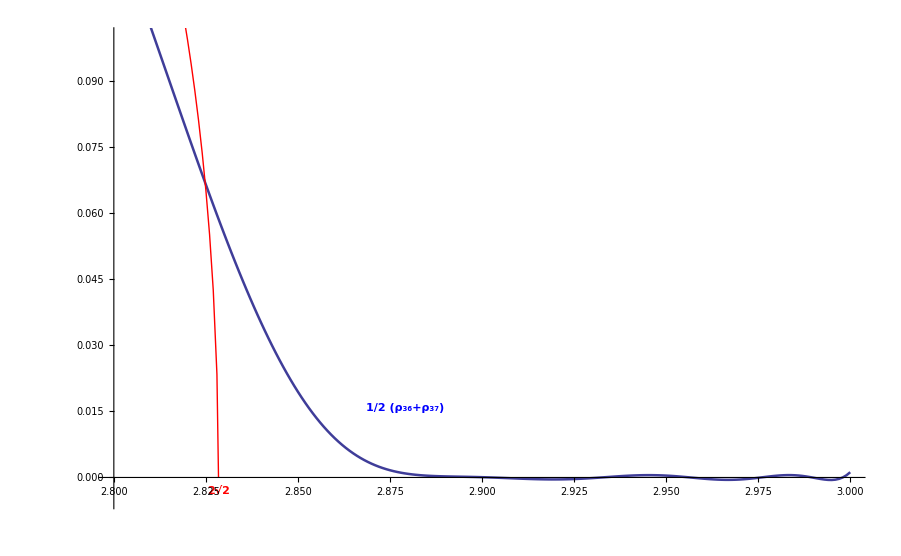

```mathematica
Show[ListPlot[Table[{x,ρFree[x]},{x,3.43,3.5,1/10000}],Joined->True,PlotStyle->{Red},PlotRange->{{2.8,q+1},{-.005,.10}},AxesOrigin->{2.8,0},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotRange->{2.8,q+1}],
ListPlot[(ρLebesgueGraphTail+ρLebesgueGraphTailNminus1)/2//N,AxesOrigin->{27/10,0},Joined->True,PlotStyle->{Thickness[.002]},AxesStyle->{Directive[Black,12,Thickness[.02]],Directive[Black,Thickness[.02]]}],
Graphics[{Blue,Text[Style[HoldForm[1/2(Subscript[ρ, 36]+Subscript[ρ, 37])],Large,Bold],Evaluate[ρLebesgueGraphTail⟦170⟧+{.01,.01}]]}],
Graphics[{Red,Text[Style[HoldForm["2√2"],Medium,Bold],{2Sqrt[2],-.003}]}],
ListPlot[Join[Table[{x,ρFree[x]},{x,28/10,Sqrt[8],1/1000}],{{2Sqrt[2],0}}],Joined->True,PlotStyle->{Red},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}]]
```